```mathematica
c1= Plot[Sqrt[-x^2 + 4] , {x, -4, 4}, AspectRatio->Automatic]
c2 = Plot[-Sqrt[-x^2 + 4] , {x, -4, 4}, AspectRatio->Automatic]
c1
c1
```

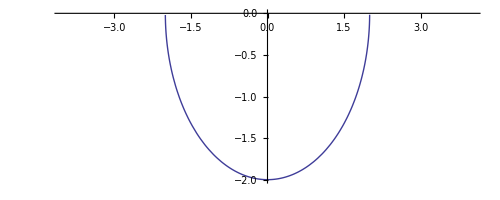

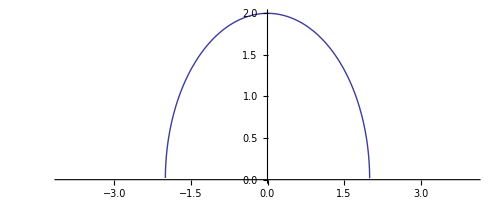

-Graphics-

```mathematica
-Sqrt[-x^2 + 4] , {x, -4, 4}
```

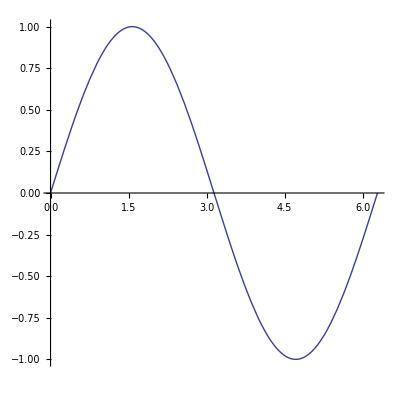

```mathematica
Plot[Sin[θ], {θ, 0, 2 Pi}, AspectRatio->1]
```

```mathematica
F : ℝ->ℝ
F
```

F:ℝ→ℝ

F

```mathematica
ListPlot[Table[{2*Cos[t], 2*Sin[t]}, {t, 0, 2*Pi, Pi/100}], AspectRatio->Automatic, Joined->True, ColorFunction->"Rainbow"]
```

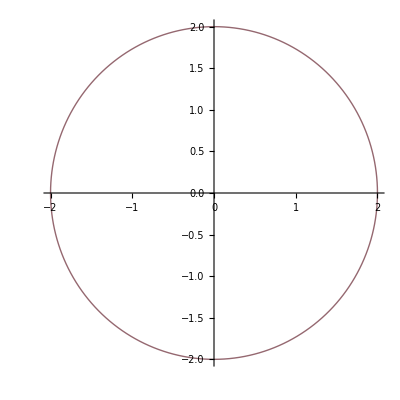
```mathematica
-Graphics-

CountryData["World", "Shape"]
```

-Graphics-

```mathematica
Plot[{-Sqrt[-x^2 + 4] , Sqrt[-x^2 + 4]} , {x, -2,2}, AspectRatio->Automatic]
```

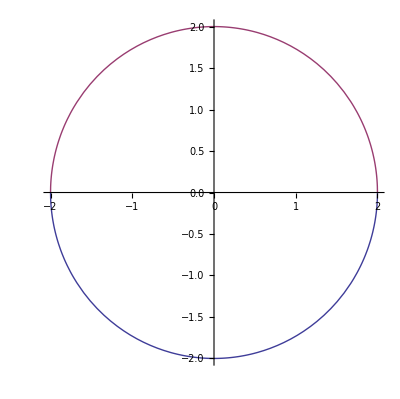
```mathematica
-Graphics-

Manipulate[ParametricPlot[{2 Cos[θ], -2 Sin[θ]}, {θ, 0, a}, PlotRange-> {{-2,2}, {-2,2}}], {a, 0, 2 Pi}]
```

-Graphics-

ParametricPlot::plld: Endpoints for θ in {θ, 0, FE`a$$91} must have distinct machine-precision numerical values.

```mathematica
Manipulate[ParametricPlot[{2 Cos[θ], -2 Sin[θ]}, {θ, Pi/2, a}, PlotRange->{-2,2}, {-2,2}}], {a, Pi/2, 2 Pi + Pi/2}]
```

```mathematica
Manipulate[ParametricPlot[{2 Cos[θ], 2 Sin[θ]}, {θ, Pi/2, a}, PlotRange-> {{-2,2}, {-2,2}}, ColorFunction->"Rainbow"], {a, Pi/2, 2 Pi + Pi/2}]
```

```mathematica
v = 20
θ = Pi/4
```

20

π/4

```mathematica
h = 6
```

6

```mathematica
Manipulate[ParametricPlot[{v Cos[θ] t , v Sin[θ] t - 1/2 * 9.8 * (t)^2 + h }, {t, 0, a}, PlotRange-> {{0,50 }, {0,15+h}}, ColorFunction->"Rainbow"], {a, 0, (2 *v  * Sin[θ])/9.8  + 1}]
```

ParametricPlot::plld: Endpoints for t in {t, 0, FE`a$$53} must have distinct machine-precision numerical values.

ParametricPlot::prng: Value of option PlotRange -> {{0, 50}, {0, 15 + h}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.